```mathematica
H=({{a, -I*b*e^(-I*θ), -I*b*Cos[θ]}, {I*b*e^(I*θ), -a, 0}, {I*b*Cos[θ], 0, -a}})
```

{{a,-ⅈ b e^(-ⅈ θ),-ⅈ b Cos[θ]},{ⅈ b e^(ⅈ θ),-a,0},{ⅈ b Cos[θ],0,-a}}

```mathematica
FullSimplify[Eigenvalues[H]]
```

{-a,-√(a^2+(3 b^2)/2+1/2 b^2 Cos[2 θ]),√(a^2+(3 b^2)/2+1/2 b^2 Cos[2 θ])}

```mathematica
Eigenvectors[H]
```

{{0,-e^(ⅈ θ) Cos[θ],1},{(ⅈ (-2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-1/2 e^(ⅈ θ) (-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ],1},{-(ⅈ (2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-1/2 e^(ⅈ θ) (-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ],1}}

```mathematica
H1=({{a, -I*b*(Cos[θ]-I*Sin[θ]), -I*b*Cos[θ]}, {I*b*(Cos[θ]+I*Sin[θ]), -a, 0}, {I*b*Cos[θ], 0, -a}})
```

{{a,-ⅈ b (Cos[θ]-ⅈ Sin[θ]),-ⅈ b Cos[θ]},{ⅈ b (Cos[θ]+ⅈ Sin[θ]),-a,0},{ⅈ b Cos[θ],0,-a}}

```mathematica
Eigenvalues[H1]
```

{-a,-(√(2 a^2+3 b^2+b^2 Cos[2 θ]))/(√2),(√(2 a^2+3 b^2+b^2 Cos[2 θ]))/(√2)}

```mathematica
Eigenvectors[H1]
```

{{0,-Cos[θ]/(Cos[θ]-ⅈ Sin[θ]),1},{(ⅈ (-2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-((-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ])/(2 (Cos[θ]-ⅈ Sin[θ])),1},{-(ⅈ (2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-((-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ])/(2 (Cos[θ]-ⅈ Sin[θ])),1}}

```mathematica
H3=({{a, -I*b*(x-I*y), -I*b*x}, {I*b*(x+I*y), -a, 0}, {I*b*x, 0, -a}})
```

{{a,-ⅈ b (x-ⅈ y),-ⅈ b x},{ⅈ b (x+ⅈ y),-a,0},{ⅈ b x,0,-a}}

```mathematica
Eigenvalues[H3]
```

{-a,-√(a^2+2 b^2 x^2+b^2 y^2),√(a^2+2 b^2 x^2+b^2 y^2)}

```mathematica
Eigenvectors[H3]
```

{{0,-x/(x-ⅈ y),1},{(ⅈ (-a+√(a^2+2 b^2 x^2+b^2 y^2)))/(b x),-(-x-ⅈ y)/x,1},{-(ⅈ (a+√(a^2+2 b^2 x^2+b^2 y^2)))/(b x),-(-x-ⅈ y)/x,1}}

```mathematica
M0=-1
M1=1
A1=0.5
```

-1

1

0.5

```mathematica
Plot3D[{-(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]])),-Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]]))^2+2*A1^2*Sin[Subscript[k, x]]^2+A1^2*Sin[Subscript[k, y]]^2],Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]]))^2+2*A1^2*Sin[Subscript[k, x]]^2+A1^2*Sin[Subscript[k, y]]^2]},{Subscript[k, x],-Pi,Pi},{Subscript[k, y],-Pi,Pi}]
```

-Graphics3D-

```mathematica
-Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]]))^2+2*A1^2*Sin[Subscript[k, x]]+A1^2*Sin[Subscript[k, y]]^2]
```

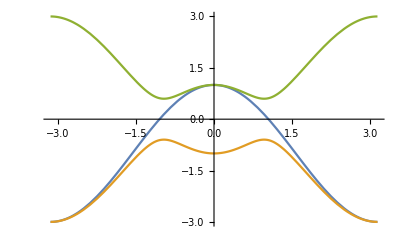

```mathematica
Plot[{-(M0+2*M1(1-Cos[Subscript[k, x]])),-Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]]))^2+2*A1^2*Sin[Subscript[k, x]]^2],Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]]))^2+2*A1^2*Sin[Subscript[k, x]]^2]},{Subscript[k, x],-Pi,Pi}]
```